# Riemann Sum

Approximating the definite integral

## Explanation

Let’s suppose you want to obtain the area under the curve in a plot

Example curve and area

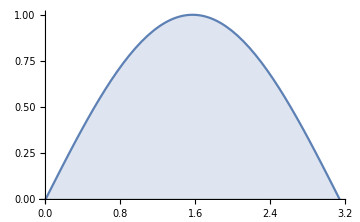
-Graphics-
Actual area: 2.

```mathematica
area = NIntegrate[Sin[x], {x, 0, Pi}];
Grid[{
{functionPlot :=Plot[Sin[x], {x, 0, Pi}, Filling->Axis, ImageSize->Medium]; functionPlot},
{"Actual area: " <> ToString[area//N]}
}]
```

If you were drawing the curve in paper, it is not really possible to measure it directly as it is. The most naive approach is to draw geometrical figures to which is know how to calculate their area. For example, rectangles.

Representing the curve as rectangles

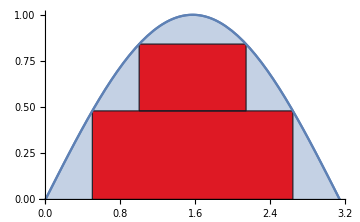
-Graphics-
Rectangle area 1.44004
Actual area 2.
Error 0.559957

```mathematica
rectCoord = {
{{0.5,0},{Pi-0.5,0},{Pi-0.5, Sin[0.5]},{0.5,Sin[0.5]}},
{{1.0, Sin[0.5]},{Pi-1,Sin[0.5]},{Pi-1,Sin[1]},{1,Sin[1]}}
};
bars =Map[ Graphics[{
		EdgeForm[{Thickness[Medium], Black}],
		Red,
		Polygon[#]
}]&,
rectCoord
];
rectArea =  Plus @@ Map[Area @ Polygon[#]&, rectCoord];
error := Abs[area-rectArea];
Grid[{
{Show[Flatten[{functionPlot, bars, functionPlot}], ImageSize->Medium]},
{"Rectangle area " <> ToString[rectArea // N]},
{"Actual area " <> ToString[area // N]},
{"Error " <> ToString[error // N]}
}]
```

We can simplify our approximation making rectangle’s height be dependant of the curve’s values, for example

Now the rectangle height depends on the curve height

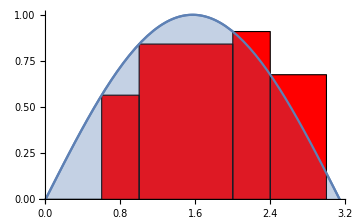
-Graphics-
Rectangle area 1.83632
Actual area 2.
Error 0.163675

```mathematica
rectXCoord = {
	{0,0.6},
	{0.6,1},
	{1,2},
	{2,2.4},
	{2.4, 3}
};
bars =Map[ 
Graphics[{
	EdgeForm[{Thickness[Medium], Black}],
	Red,
	Polygon[{{#[[1]],0},{#[[2]],0},{#[[2]], Sin[#[[1]]]},{#[[1]], Sin[#[[1]]]}}]
}]&,
rectXCoord
];
rectArea = Plus @@ Map[
	(#[[2]] - #[[1]]) * Sin[#[[1]]]&,
	rectXCoord
];
Grid[{
	{Show[Flatten[{functionPlot, bars, functionPlot}],ImageSize->Medium]},
	{"Rectangle area " <> ToString[rectArea // N]},
	{"Actual area " <> ToString[area // N]},
	{"Error " <> ToString[error // N]}
}]
```

In this example, the height is equal to the value of the function in the x value of the left-most side of the rectangle. The total area of the rectangles with this approach is:

∑_(x∈X) f(x_Left) * (x_Right - x_Left)

where the elements in X contain the positions of the left-most and right-most sides of each rectangle

To make or approximation even more simple to calculate, we can make all rectangles to have the same width and to assure all rectangles are adjacent with each other

```mathematica
(*Obtains the area of all rectangles in the Riemann sum*)
riemannArea [function_, start_, end_, rectNumber_, type_String:"Left"]:= Plus @@ Table [
	(end - start) / rectNumber * Switch[
		type,
		"Left",
		function[x],
		"Right",
		function[x + (end - start) / rectNumber],
		"Mean",
		(function[x] + function[x + (end - start) / rectNumber]) / 2.0
	],
	{x, start, end - (end - start) / rectNumber, (end - start) / rectNumber}
];
```

```mathematica
(*Draws the plot and rectangles for the Riemann sum*)
riemannGraphic[function_, start_, end_, rectNumber_Integer, type_String:"Left"] := 
Show[{
	RectangleChart[ 
		Table[
			{
				(end - start) / rectNumber,
				Switch[
					type,
					"Left",
					function[x],
					"Right",
					function[x + (end - start) / rectNumber],
					"Mean",
					(function[x] + function[x + (end - start) / rectNumber]) / 2.0
				]
			},
			{x, start, end - (end - start) / rectNumber, (end - start) / rectNumber}
		],
		BarSpacing->None,
		ChartStyle->Red,
		ImageSize->Medium
	],
	Plot[function[x], {x, start, end}, Filling->Axis, ImageSize->Medium]
}];
```

Covering the curve with rectangles of the same width

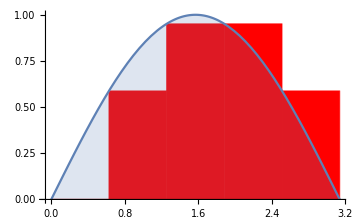
-Graphics-
Rectangle area 1.93377
Actual area 2.
Error 0.0662344

```mathematica
rectArea = riemannArea[Sin, 0, Pi, 5];
Grid[{
{riemannGraphic[Sin, 0, Pi, 5]},
{"Rectangle area " <> ToString[rectArea // N]},
{"Actual area " <> ToString[area // N]},
{"Error " <> ToString[error // N]}
}]
```

In this case the total area of the rectangles equals to:

∑_(i = 1)^n f(x_i) Δx

where n is the number of triangles and x_i is the position and Δx is the width of the rectangles.

## Approaching the error to zero

There are many parts of the curve that are still not covered by the rectangles, this can improve if we use more rectangles of smaller size

Trying with a smaller rectangle width

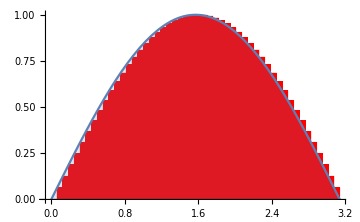
-Graphics-
Rectangle area 1.99934
Actual area 2.
Error 0.000658017

```mathematica
rectArea = riemannArea[Sin, 0, Pi, 50];
Grid[{
{riemannGraphic[Sin, 0, Pi, 50]},
{"Rectangle area " <> ToString[rectArea // N]},
{"Actual area " <> ToString[area // N]},
{"Error " <> ToString[error // N]}
}]
```

The rectangle height doesn’t necessarily have to be the value of the curve on the left side, it can also use the right side or the mean of both. These are the most common methods.

Showing a graph with variable rectangle quantity and method and calculating the total area of the rectangles, the curve and comparing their difference

```mathematica
Manipulate[
Grid[{
{riemannGraphic[Sin, 0, Pi, rectangles, mode]},
{
rectArea = riemannArea[ Sin, 0, Pi, rectangles, mode];
"Riemann area: " <>ToString[rectArea // N]
},
{"Actual area " <> ToString[area // N]},
{"Error " <> ToString[error // N]}
}],
{rectangles, 1,50,1},
{mode, {"Left","Right", "Mean"}}
]
```

As you can see, the more rectangles you add, the lesser the error is. In fact the error tends to zero as the number of rectangles of equal width tend to infinite.

Plot to the error given the number of rectangles

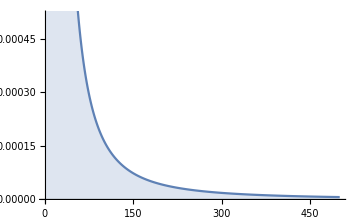

```mathematica
DiscretePlot[Abs[area - riemannArea[Sin, 0, Pi, r]],{r, 1, 500,1}, ImageSize -> Medium]
```

Given how the Riemann sum converges with the area under a curve, it is useful as an approximation for the definite integral.

Further Explorations

Definite integral

Lebesgue integration

Authorship information

Itzel Carolina Delgadillo Perez

June 22nd 2017

caroagsmex@hotmail.com